# Chain Rule from Calculus 3

## Gradient of f:ℝ^n→ℝ

A function f:ℝ^n→ℝ is of the form f_1(x_1,…,x_n) and the gradient is the function
	∇_x f=((∂f_1)/(∂x_1),…,(∂f_1)/(∂x_n))
in other words ∇_x f:ℝ^n→ℝ^n.  The gradient is the straight uphill direction it is perpendicular to contour lines and surfaces.

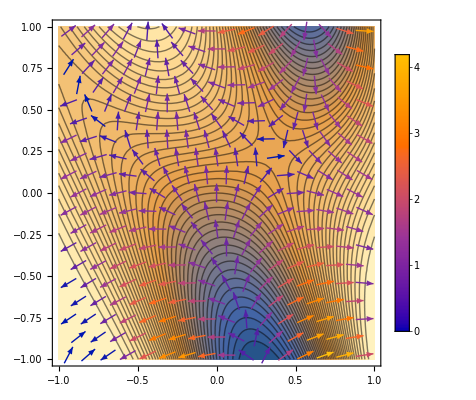

```mathematica
Clear[f,g,x1,x2]
f[{x1_,x2_}]:=Sin[x1^2+x2 Cos[ x2 +3x1]]
g[{x1_,x2_}]=Grad[f[{x1,x2}],{x1,x2}];
Show[
ContourPlot[f[{x1,x2}],{x1,-1,1},{x2,-1,1},Contours->40],
VectorPlot[g[{x1,x2}],{x1,-1,1},{x2,-1,1}, PlotLegends->Automatic]]
```

```mathematica
Clear[f,g,x1,x2,x3]
f[{x1_,x2_,x3_}]:=Sin[x1^2+x2 Cos[ x2 +3x1 +x3 x2]]
g[{x1_,x2_,x3_}]=Grad[f[{x1,x2,x3}],{x1,x2,x3}];
Show[
ContourPlot3D[f[{x1,x2,x3}],{x1,-1,1},{x2,-1,1},{x3,-1,1},Contours->2],
VectorPlot3D[g[{x1,x2,x3}],{x1,-1,1},{x2,-1,1}, {x3,-1,1},PlotLegends->Automatic]]
```

-Graphics3D-

```mathematica
Clear[f,g,x1,x2,x3]
f[{x1_,x2_,x3_}]:=Sin[x1^2+x2 Cos[ x2 +3x1 +x3 x2]]
g[{x1_,x2_,x3_}]=Grad[f[{x1,x2,x3}],{x1,x2,x3}];
Show[
SliceContourPlot3D[f[{x1,x2,x3}],"CenterPlanes",{x1,-1,1},{x2,-1,1},{x3,-1,1},Contours->20],
SliceVectorPlot3D[g[{x1,x2,x3}],"CenterPlanes",{x1,-1,1},{x2,-1,1}, {x3,-1,1},PlotLegends->Automatic]]
```

-Graphics3D-

```mathematica
?VectorPlot3D
```

## Gradient of f:ℝ^n→ℝ^m

A function f:ℝ^n→ℝ^m is of the form (f_1(x_1,…,x_n) 
f_2(x_1,…,x_n)
⋮
f_m(x_1,…,x_n))and the gradient is the function
	∇_x f=((∂f_1)/(∂x_1),…,(∂f_1)/(∂x_n)
(∂f_2)/(∂x_1),…,(∂f_2)/(∂x_n)
⋮
(∂f_m)/(∂x_1),…,(∂f_m)/(∂x_n))=(∂f_i)/(∂x_j)
in other words ∇_x f:ℝ^n→ℝ^(m×n).  The gradient is the local linearization.  The gradient is an m×n matrix which is usually called the Jacobian!   See https://en.wikipedia.org/wiki/Jacobian_matrix_and_determinant for more reminders!

## Multivariable Chain Rules

Chain rules let us differentiate compositions f(g(x)) see https://en.wikipedia.org/wiki/Chain_rule#Multivariable_case for more words.

### f:ℝ^p→ℝ^m and g:ℝ^n→ℝ^p so that h=f∘g:ℝ^n→ℝ^m

So ∇_x h:ℝ^n→ℝ^(m×n) and has to be some combination of the partials of the constituent functions.  In Calculus 3 you probably gave the middle variable a name say y=g(x) and thought about adding up all the appropriate chain rule fragments. It is simply
	∇_x h(x)=∇_y f(g(x)) ∇_x g(x)
In words, differentiate the outside function (evaluate at the inside function) and multiply by the derivative of the inside function.  The multiplication is a matrix-matrix multiplication and because matrix multiplication does not commute the order matters.

The way to check this …